基礎庫 :

```mathematica
<<(FileNameJoin[{$UserDocumentsDirectory,"Wolfram Mathematica","snslib.wl"}])
```

WorkPath :

```mathematica
SetDirectory["D:\\Work\\SSR\\basePlan"];
dataPath = FileNameJoin[{ParentDirectory[],"_data"}]
```

D:\Work\SSR\_data

## 数值尺度

令：Tv(res)与Tv(Lv)*lv成反比
Tv(res) =  tvPara / (Lv * Tv(Lv))

```mathematica
ClearAll[resconfig,bdNum,tvPara,resSpeed,resByLv];
resconfig = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"resource","base"];
bdNum[type_,lv_]:= First[FirstPosition[ToExpression[productconfig[SelectFirst[#type==type&],"build"]],n_/;lv<n,{5}]]-1;
tvPara[type_]:= getDayByLv[maxLv]*maxLv/(10000*resconfig[SelectFirst[#type==type&],"total"]);
resSpeed[type_,lv_]:= Module[{step=funcsLTStep/.Private`x->lv},(getDayByLv[lv+1]*(lv+1)-getDayByLv[lv]*lv)/(tvPara[type]*step)]; 
resByLv[type_,lv_Integer]:= Sum[resSpeed[type,n]*funcsLTStep/.Private`x->n,{n,1,lv-1}];
resByLv[type_,lv_Real]:= resByLv[type,IntegerPart@lv]+(resByLv[type,IntegerPart@lv+1]-resByLv[type,IntegerPart@lv])*FractionalPart@lv;
```

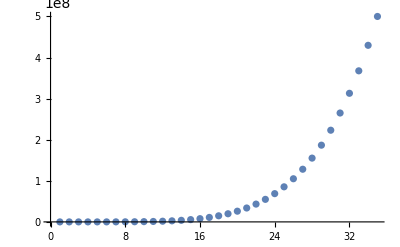

```mathematica
ListPlot[Table[resByLv["r1",n],{n,1,maxLv}]]
```

## 生产

科技/英雄/vip: 线性乘法, 斜率=advanceParam

```mathematica
ClearAll[productconfig,productHours,bdNum,productBaseHour,productTotal,advanceParam,advanceParams];
productconfig =  Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"resource","product"];
productHours = Table[24*funcsLTStep/.Private`x->n,{n,1,maxLv-1}];
bdNum[type_,lv_]:= First[FirstPosition[ToExpression[productconfig[SelectFirst[#type==type&],"build"]],n_/;lv<n,{5}]]-1;
productBaseHour[type_,lv_]:= Round[resconfig[SelectFirst[#type==type&],"product"]*productconfig[SelectFirst[#type==type&],"base"]*resSpeed[type,lv]/24,10];
productTotal[type_,lv_]:= Sum[productBaseHour[type,n]* bdNum[type,n]*productHours[[n]],{n,1,lv-1}];
advanceParam[type_,channel_] := Solve[Table[productBaseHour[type,n]*(n-1)*x*bdNum[type,n],{n,2,maxLv-1}].productHours[[2;;]]== productconfig[SelectFirst[#type==type&],channel]*productTotal[type,maxLv],x][[1,1,2]];
advanceParams= Dataset@Association@Thread[Normal@resconfig[All,"type"]->Association[Thread[{"study","hero","vip"}->#]&/@Outer[advanceParam,Normal@resconfig[All,"type"],{"study","hero","vip"}]]];
```

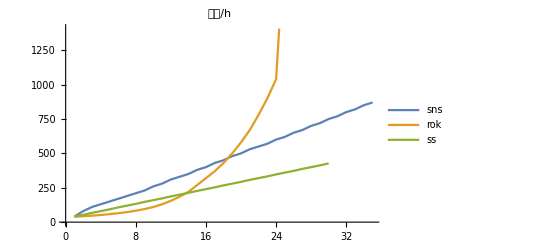

```mathematica
fucRok = Normal@Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"other_data","rok"][All,"res_product"];
fucSS = Normal@Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"other_data","ss"][All,"res_product"];
ListLinePlot[{Table[productBaseHour["r4",n],{n,1,maxLv}],productBaseHour["r4",1]/fucRok[[1]]*fucRok,productBaseHour["r4",1]/fucSS[[1]]*fucSS},PlotLegends->{"sns","rok","ss"},PlotLabel->"产量/h"]
```

```mathematica
exportData =Association@@( Table[snsGetIdByString["attrgroup-build",Base`excleLookUp[resconfig,"type"->#,"attr"]<>ToString@n]-><|"数值0"->productBaseHour[#,n],"数值1"->productBaseHour[#,n]*12|>,{n,1,maxLv}]&/@Normal[resconfig[All,"type"]]);
```

```mathematica
snsExportTable["attrgroup-build.csv",snsUpdateTable["attrgroup-build",exportData]]
```

C:\k-config\excel\attrgroup-build.csv

## 采集

collectTotal=Sum[base[lv]*hours[lv]*troopNum[lv]/resnum[lv],{1,maxLv}]

```mathematica
ClearAll[collectconfig,troopNum,resNum,collectHours,collectAdvanceParam,collectAdvanceParams];
collectconfig =  Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"resource","collection"];
troopNum[lv_]:= Base`excleLookUp[collectconfig,"lv"-> lv,"troopNum"];
resNum[lv_]:=FirstPosition[resconfig[First/@ToExpression[#]&,"build"],n_/;n> lv,{5}][[1]]-1;
collectHours = Table[Base`excleInterpolation[collectconfig,"lv"-> n,"hours"]*funcsLTStep/.Private`x->n,{n,1,maxLv-1}];
collectBaseHour[type_,lv_]:= Round[resconfig[SelectFirst[#type==type&],"collect"]*collectconfig[SelectFirst[#type==type&],"base"]*resSpeed[type,maxLv]/24,10];
collectTotal[type_,lv_]:= Sum[collectBaseHour[type,n]* troopNum[n]*collectHours[[n]]/resNum[n],{n,1,lv-1}];
collectAdvanceParam[type_,channel_] := Solve[Table[collectBaseHour[type,n]*(n-1)*x*troopNum[n]/resNum[n],{n,1,maxLv-1}].collectHours == collectconfig[SelectFirst[#type==type&],channel]*collectTotal[type,maxLv],x][[1,1,2]];
collectAdvanceParams= Dataset@Association@Thread[Normal@collectconfig[All,"type"]->Association[Thread[{"study","hero","vip"}->#]&/@Outer[collectAdvanceParam,DeleteCases[Normal@collectconfig[All,"type"],""],{"study","hero","vip"}]]];
```

## 产出数据

```mathematica
ClearAll[otherParam,resData,resGetByLv];
otherParam[type_] := Solve[Sum[(funcsLTStep/.Private`x->n)*x*(n-1),{n,2,maxLv-1}]== 10000*Times@@Base`excleLookUp[resconfig,"type"->type,{"total","other"}],x][[1,1,2]];
resData[type_,lv_]:= Module[{x,baseTime=(funcsLTStep/.Private`x->lv),getParam},getParam[fuc_,channel_]:= fuc[type,channel]*(lv-1);<|"lv"->lv,"base"->resSpeed[type,lv],"baseTime"->baseTime,"productBaseHour"-> productBaseHour[type,lv],"bdNum"->bdNum[type,lv],"productStudy"-> getParam[advanceParam,"study"],"productHero"-> getParam[advanceParam,"hero"],"productVip"-> getParam[advanceParam,"vip"],"productHours"->productHours[[lv]],"productTotal"->productBaseHour[type,lv]*bdNum[type,lv]*productHours[[lv]]*(1+Total[getParam[advanceParam,#]&/@{"study","hero","vip"}]),"collectBaseHour"->collectBaseHour[type,lv],"troopNum"->troopNum[lv],"resNum"-> resNum[lv],"collectStudy"-> getParam[collectAdvanceParams,"study"],"collectHero"-> getParam[collectAdvanceParams,"hero"],"collectVip"-> getParam[collectAdvanceParams,"vip"],"collectHours"-> collectHours[[lv]],"collectTotal"->collectBaseHour[type,lv]*troopNum[lv]/resNum[lv]*collectHours[[lv]]*(1+Total[getParam[collectAdvanceParams,#]&/@{"study","hero","vip"}]) ,"other"-> otherParam[type]*(lv-1)|>];
resGetByLv[type_,lv_]:= Module[{data=Dataset@resData[type,lv]},<|"product"->data[#productTotal&],"collect"->data[#collectTotal&],"other"->data[#other*#baseTime&]|>];
```

```mathematica
Export[FileNameJoin[{dataPath,#<>"_"<>"resData.txt"}],Table[resData[#,n],{n,1,maxLv-1}]//Dataset,"Table"]&/@resconfig[All,"type"]
```

## 消耗

积累 = 产出/消耗 分段函数(波折)：

```mathematica
ClearAll[resGetData,resConsumeConfig,funcsAccumulate,resAccumulate,resConsume,consumeData];
resGetData= Association@@(#->SemanticImport[FileNameJoin[{dataPath,#<>"_"<>"resData.txt"}]]&/@{"r1","r2","r3","r4"});
resConsumeConfig = Association@@(#->Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"resource",#]&/@{"r1","r2","r3","r4"});
funcsAccumulate =  Association@@(#->Prepend[Table[Fit[Normal/@Values/@{resConsumeConfig[#][n,{"lv","accumulate"}],resConsumeConfig[#][n+1,{"lv","accumulate"}]},{1,x},x],{n,1,Length@consumeconfig-1}],x]&/@{"r1","r2","r3","r4"});
resAccumulate[type_,lv_]:= funcsAccumulate[type][[Base`excleIndex[resConsumeConfig[type],"lv"-> lv]]]/.x->lv;
resConsume[type_,lv_]:= (Last@Accumulate@Normal@resGetData[type][Range[lv],#productTotal+#collectTotal+#baseTime*#other&])/resAccumulate[type,lv];
consumeData[type_String,lv_]:=Module[{output =Total@Values@resGetByLv[type,lv], base=If[lv≤1,resConsume[type,1],resConsume[type,lv]-resConsume[type,lv-1]],config=resConsumeConfig[type]},<|"lv"-> lv,"output"->output,"base"-> base,"accumulate"->If[base==0,0,output/base],(#->base*Base`excleLookUp[{config,"lv"-> lv},{config,#}])&/@Normal[config[First,Keys]][[3;;]]|>];
```

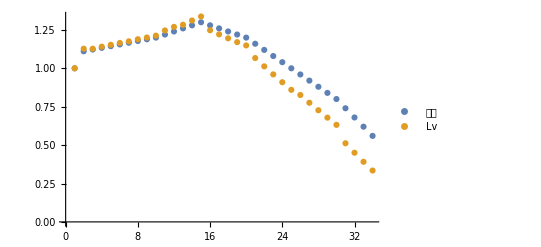

```mathematica
ListPlot[Transpose@Table[{resAccumulate["r1",n],consumeData["r1",n]["accumulate"]},{n,1,maxLv-1}],PlotLegends->{"累积","Lv"}]
```

```mathematica
Export[FileNameJoin[{dataPath,#<>"_"<>"consumeData.txt"}],Table[consumeData[#,n],{n,1,maxLv-1}]//Dataset,"Table"]&/@resconfig[All,"type"]
```